```mathematica
fullSimplifyReal[x_]:=Assuming[_Symbol ∈ Reals , FullSimplify@x]
myFormatConvertToNegativePowers = StandardForm[#/.Power[expr_, r_?Negative] :> Superscript[expr,r] ]&;

CL=2.997925 10^10;
Gr=6.67 10^-8;
ARAD=7.56464 10^(-15);

KPE=0.4;
KPDUST = 1;       (* dust kappa *)

SGT=6.6524 10^-25; (*Thomson cross section cm^2*)
RGAS=8.31 10^7;
KB=1.38062 10^-16;
PC=3.085678 10^18;
Msol=1.989 10^33;
MBH=10^7 Msol;
MP=1.672661 10^-24;
SGB = ARAD*CL/4;
DAY = 24 3600;
YR=31536000;
MsolYr = Msol/YR;
KM=10^5;

rulzGlob = {α->0.1, ϵ->0.1, η->0.1, Subscript[T, s]->T0, T0->1500, κ->kap, M->MBH, kpc->1, μ->1,
			G->Gr, Rgas->RGAS, a->ARAD, c->CL};
			


rulForConst={J->1, m->1,Rg->RGAS, σ->SGB,G->Gr,c->CL, a->ARAD};

CalculateMdotNumber[rul_, excess_] := Module[{res},
	res =excess* μ η ϵ^-1 4Pi CL Gr M /KPE/CL^2/.rul]
```

```mathematica
CalculateMdotNumber[{ ϵ->0.1 Subscript[ϵ, 0.1], η->0.1 Subscript[η, 0.1],M->MBH Subscript[M, 7]}, 1]/MsolYr
```

(0.0220425 M_7 η_0.1)/(ϵ_0.1)

EqHoriz = Σ ν -Mdt/(3π) J

ρ ν = -2/3..

ρ^(1/3) =Ω^2/(8K)z^2+C,



σ_2 =(16/35) ρ^+ z_b

	     T_s^4 = T_d^4 + (3Mdt Ω^2)/(4πca)
	
		ρ^-= aT_d^4/(3 R_g T_s)

Gaslayer,verticalbalance:

P_s-P_0=-Ω^2 ρ̄  z_s^2,

	   R_g(ρ^-T_s-ρ_c T_c)=-Ω^2 ρ̄  z_s^2≃-Ω^2 ρ_c z_s^2

Radiation transfer I:


(∂F)/(∂z) =3/8 Ω^2 Ṁ ρ ,
	
	   F^+ = 3/8 Md Ω^2 = 3/8 F_0

Radiation transferII:


E=(2 F)/c (1 + 3/2τ), it already includes BC at the photosphere

	   τ_s= κ_d σ_2= (8 acT_d^4)/(9 F_0)=acT_d^4/(3 F^+), F_0= Md Ω^2

		σ_2  =acT_d^4/(3 F^+κ_d), and  σ_2  = 16/35 ρ^+z_b, finally:

		ρ^+z_b =35/16 acT_d^4/(3 κ_d F^+)

Solving rad transfer from z_s to 0:

a T_c^4=3 F^+/c(κ_e σ_1+2/3)-(a T_d^4)/2

### Things that don' t require solution of equations:

```mathematica
(*F^+ ->  3/8 Mdt  Ω^2*)
```

```mathematica
(*1.*)


Eq1 = Subscript[T, c]^4 - 3 SuperPlus[F]/(a c)(Subscript[κ, c] Subscript[z, s] Subscript[ρ, c] + 2/3) + Subscript[T, d]^4/2
P1 = (a Subscript[T, d]^4)/3;
Eq7 = Subscript[z, s] Subscript[ρ, c]- 4/9 SuperPlus[F]/(α Ω Rgas Subscript[T, c]);



(*2*)

EqZs = Solve[Eq7==0,  Subscript[z, s]]

EqTc = Part[Eq1/.EqZs//Together//Numerator,1];

(*HiPowTc = *)
EqTc=Assuming[Subscript[ρ, c]>0 ∧ Rgas>0 ∧ α>0 ∧ Subscript[T, c]>0, 
	fullSimplifyReal[Cancel[EqTc/Coefficient[EqTc,Subscript[T, c], 5]]]]/.{Subscript[T, c]->T,Subscript[T, d]->T0,Subscript[κ, c]->kpc};

EqTcFun = Module[{A5, A0, A1, A},
	A = CoefficientList[EqTc,Subscript[T, c]]
	]
	



Clear[P1,Eq1,Eq7,VertFlx]
(*/.F^+->VertFlx/.Ω -> G^(1/2) M^(1/2) r^(-3/2)*)
(*//Together//Numerator*)

(*solRoc = Solve[EqRoc==0, Subscript[ρ, c]]*)

(*Refine[solTc,{Subscript[ρ, c]>0,Subscript[ρ, s]>0,Subscript[ρ, s]<Subscript[ρ, c],α>0,Subscript[R, g]>0,Subscript[T, c]>0,F^+>0}][[1]]//fullSimplifyReal*)
(*tmp=Assuming[Subscript[ρ, c]>Subscript[ρ, s] ∧ Rgas>0 ∧ α>0,fullSimplifyReal[solTc]]
ClearAll[tmp]
*)
(*tmp[[1]][[1]][[2]]
Select[Values[tmp], #>0 &  ] *)
```

T_c^4+T_d^4/2-(3 (2/3+z_s κ_c ρ_c) F^+)/(a c)

{{z_s→(4 F^+)/(9 Rgas α Ω T_c ρ_c)}}

{T^5-(4 kpc (F^+)^2)/(3 a c Rgas α Ω)+1/2 T (T0^4-(4 F^+)/(a c))}

```mathematica
(* Mid-plane temperature Subscript[T, c]*)
VertFlx = 3/8 Mdt Ω^2;
ClearAll[DiskTcFun,EqTcMod,rulz,EqTcCoeffs]

EqTc

EqTcMod=EqTc/.{Subscript[T, c]->T,Subscript[T, d]->T0,Subscript[κ, c]->kpc, SuperPlus[F]->VertFlx}/.Ω -> G^(1/2) M^(1/2) r^(-3/2) 


EqTcCoeffs[r_,rulz_] := Module[{CoefTc, tmp},

	CoefTc = CoefficientList[EqTc,T]/.{SuperPlus[F]->VertFlx}/.Ω -> G^(1/2) M^(1/2) r^(-3/2);

	CoefTc/.rulz
	
	]

EqTcCoeffs[x, rulz]

DiskTcFunDisk[CoefList_]:=Module[{solT},
	solT = Sum[CoefList[[i+1]] T^i,{i,0,5}];
	solT = NSolve[solT == 0 && T>0, T, Reals]⟦1⟧⟦1⟧⟦2⟧
	]


ClearAll[rulz,A,EqTcMod]
```

T^5-(4 kpc (F^+)^2)/(3 a c Rgas α Ω)+1/2 T (T0^4-(4 F^+)/(a c))

T^5+1/2 T (-(3 G M Mdt)/(2 a c r^3)+T0^4)-(3 G^(3/2) kpc M^(3/2) Mdt^2)/(16 a c r^(9/2) Rgas α)

ReplaceAll::reps: {rulz} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{-(3 G^(3/2) kpc M^(3/2) Mdt^2)/(16 a c Rgas x^(9/2) α),1/2 (T0^4-(3 G M Mdt)/(2 a c x^3)),0,0,0,1}/.rulz

0.0220425 μ$11197

Mdot = 1.39024×10^24

F^+=213.599

T^5-(4 kpc (F^+)^2)/(3 a c Rgas α Ω)+1/2 T (T0^4-(4 F^+)/(a c))

{21692.7,18638.2,16369.,14613.5,13213.2,12068.9,11115.4,10308.,9615.22,9013.84,8486.65,8020.54,7605.31,7232.94,6897.01,6592.34,6314.7,6060.57,5827.04,5611.65,5412.34,5227.32,5055.09,4894.34,4743.93,4602.87,4470.29,4345.44,4227.63,4116.28,4010.84,3910.85,3815.88,3725.55,3639.51,3557.46,3479.1,3404.19,3332.49,3263.8,3197.9,3134.63,3073.83,3015.34,2959.02,2904.75,2852.41,2801.88,2753.07,2705.89}

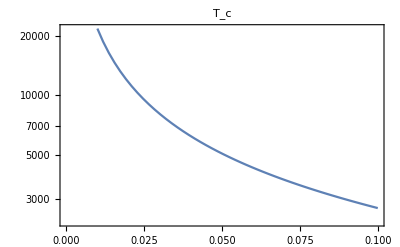

```mathematica
(*4*)

plotDiskTemp = Module[{xmin=0.01,xmax=0.1, Nx1=50, Mdot,TCoefList,fT1,
			tmp, rulz,Tgas,pltPrad,pltPgas,pltNdens,pltTemp,
			RSubAGN,l1,ymin,ymax,μ,Prad,Pgas, Tsub, Tsol,VertFlx,MdotNumber},

rulz = {α->0.1, ϵ->0.1, η->0.1,  T0->1500, M->MBH, kpc->1,
			G->Gr, Rgas->RGAS, a->ARAD, c->CL};

MdotNumber[μ_, rul_] := μ η ϵ^-1 4Pi CL Gr M /KPE/CL^2/.rul;

AppendTo[rulz, Mdt->0.2MsolYr];

Print[MdotNumber[μ, rulz]/MsolYr];

μ=1; (* exess over equilibrium value *)
Print["Mdot = ", Mdot = MdotNumber[μ, rulz]];

VertFlx = 3/8 Mdt  Ω^2 /. Ω->G^(1/2) M^(1/2) r^(-3/2);

Print["F^+=",VertFlx/.rulz/.r->PC];
Print[EqTc];
Tsol = EqTc /. Subscript[T, c]->T /.Ω->G^(1/2) M^(1/2) r^(-3/2) /. SuperPlus[F]->VertFlx/.rulz;

Tsol/.r -> x PC /. Mdt->Mdot;

X1 = Range[xmin,xmax,(xmax-xmin)/(Nx1-1)];

TCoefList[x_]:= EqTcCoeffs[x,rulz];

fT1 = TCoefList /@ (PC X1);   (* equatorial T *)

fT1 = DiskTcFunDisk[#]& /@ fT1;
Print[fT1];
fT1 = MapThread[{#1,#2}&, {X1, fT1}];

pltTemp = (*ListLogLogPlot*)ListLogPlot[fT1,
	Joined->True,Frame->True,
	PlotLabel->"T_c"
	]
	
]
```

## Disk mid-plane density

```mathematica
ClearAll[FunTs,FunRosWithTs,FunRos]

FunTs[r_] := (T0^4 + (3Mdt Ω^2)/(4π c a))^(1/4)/.Ω -> G^(1/2) M^(1/2) r^(-3/2)
FunRosWithTs[Ts_] := (a T0^4)/(3Rgas Ts);



FunRos[r_,rulz_] := FunRosWithTs[ FunTs[r] ]

Print[ " fiducial ρ_s and n_s " ]
FunRos[x,rulz]
%/. Mdt -> SuperPlus[F] (3/8 Ω^2)^-1/.(G M)->(x^(3/2) Ω)^2/.Rgas->Subscript[R, g]

FunRos[0.01 PC,rulz]/MP/.rulzGlob/.Mdt->0.22 MsolYr
% MP
Module[{ros2}, ros2 = (a T0^4)/(3 Rgas T0 MP)/.rulzGlob]
```

fiducial ρ_s and n_s

(a T0^4)/(3 Rgas (T0^4+(3 G M Mdt)/(4 a c π x^3))^(1/4))

(a T0^4)/(3 R_g (T0^4+(2 F^+)/(a c π))^(1/4))

5.93793×10^10

9.93214×10^-14

6.12254×10^10

```mathematica
ClearAll[EqRocFun,T, Subscript[T, d], d, Subscript[T, c], c, rulz,EqRoc];

Print["Eq5 := ", Eq5 = 2 (P1  - Rgas Subscript[T, c] Subscript[ρ, c]) + Ω^2 Subscript[z, s]^2(Subscript[ρ, c] + Subscript[ρ, s]) /. P1 -> a T0^4]

Eq5 = (2 Rgas Subscript[T, c](Subscript[ρ, s]- Subscript[ρ, c]) + Ω^2 Subscript[z, s]^2(Subscript[ρ, c] + Subscript[ρ, s]))

Eq5mod=Eq5

EqRoc = Collect[Eq5mod/.EqZs//Together//Numerator, Subscript[ρ, c]];


EqRoc = Assuming[Subscript[ρ, c]>0 ∧ Rgas>0 ∧ α>0 ∧ Subscript[T, c]>0,
			fullSimplifyReal[EqRoc/Coefficient[EqRoc, Subscript[ρ, c], 3]] ];

				
EqRoc/. Subscript[ρ, s] -> FunRos[r,rulz];
		
EqRoc = Collect[EqRoc, Subscript[ρ, c]] /. {Subscript[T, c]->T, Subscript[T, d]->T0, Subscript[ρ, c]->ρ, (*Subscript[ρ, s]->ros,*) Subscript[κ, c]->kpc};

Print["EqRoc := ",  EqRoc⟦1⟧]


EqRocFun[x_, Tc_, rulz_] := Module[{tmp},
   						tmp = EqRoc⟦1⟧ /.{ Subscript[ρ, s]->0,
   						 Subscript[ρ, s]->FunRos[r,rulz],
							SuperPlus[F]->3/8 Mdt  Ω^2 /. Ω->G^(1/2) M^(1/2) r^(-3/2)}/.{r->x,T->Tc};
							tmp=tmp/.rulz;							
							(*Print["EqRocFun=", tmp]*)
							Part[
							NSolve[tmp == 0 && ρ>0, ρ, Reals]//Flatten,
							1,2];
			
							];
							
(*rulz1 = {α->0.1, ϵ->0.1, η->0.1,  T0->1500, M->MBH, kpc->1,
			G->Gr, Rgas->RGAS, a->ARAD, c->CL,Mdt->1.3902398274104242 10^24};										
*)	
EqRocFun[0.5PC, 1000, rulzGlob]
	
rulz1=.
```

ClearAll::ssym: T_d is not a symbol or a string.

ClearAll::ssym: T_c is not a symbol or a string.

Eq5 := 2 (a T0^4-Rgas T_c ρ_c)+Ω^2 z_s^2 (ρ_c+ρ_s)

2 Rgas T_c (-ρ_c+ρ_s)+Ω^2 z_s^2 (ρ_c+ρ_s)

2 Rgas T_c (-ρ_c+ρ_s)+Ω^2 z_s^2 (ρ_c+ρ_s)

EqRoc := ρ^3-ρ^2 ρ_s-(8 ρ (F^+)^2)/(81 Rgas^3 T^3 α^2)-(8 ρ_s (F^+)^2)/(81 Rgas^3 T^3 α^2)

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

# Convective flux etc

specific heat :




	C_p=R_gas/μ(5/2+(20 P_r)/P_g+((4 P_r)/P_g)^2)  = R_gas/μ(3/2+(3(4+β)(1-β))/β^2+(4-3β)/β^2)

if  P_g=P_g then C_p =77/2≂38

	Fconv =C_p ρ(g/T)^(1/2)(Δ∇T)^(3/2)l^2/4(1+(4 P_r)/P_g)^(1/2)

	∇_ad = (1+((4+β)(1-β))/β^2)/(5/2+(4(4+β)(1-β))/β^2)

	 F^+ =  3/8 Mdt  Ω^2
	
	dTdz = -(3κ ρ F^+)/(4 a c T^3)
	dTdzad = -g ρ T/P∇_ad

```mathematica
(*Checkups   *)

(3/2+(3(4+β)(1-β))/β^2+(4-3β)/β^2)/.β->Subscript[P, g]/(Subscript[P, g]+Subscript[P, r])//Simplify//Framed
(1+((4+β)(1-β))/β^2)/(5/2+((4+β)(1-β))/β^2)/.β->1
```

5/2+(20 P_r)/P_g+(16 P_r^2)/P_g^2

```mathematica
5/2+(20 Subscript[P, r])/Subscript[P, g]+(16 Subscript[P, r]^2)/Subscript[P, g]^2/.Subscript[P, r]->Subscript[P, g]
```

```mathematica
77/2//N
```

38.5

Estimated convective flux
C_p=R_gas/μ(5/2+(20 P_r)/P_g+((4 P_r)/P_g)^2)

```mathematica
Fc=-(Subscript[C, p] ρ^2 v^3)/(Subscript[g, z] dr)1/drodT

Fc/.{Subscript[C, p]->Subscript[R, gas]/μ(5/2+(20 Subscript[P, r])/Subscript[P, g]+((4 Subscript[P, r])/Subscript[P, g])^2)  , drodT->(1+(4 Subscript[P, r])/Subscript[P, g])}/.μ->1
```

-(v^3 ρ^2 C_p)/(dr drodT g_z)

-(v^3 ρ^2 (5/2+(20 P_r)/P_g+(16 P_r^2)/P_g^2) R_gas)/(dr g_z (1+(4 P_r)/P_g))

```mathematica
ClearAll[TcEq,αDiskSolv,FconvEq,dTdzRad, dTdzAdiab,dTrad,ρ,T,z,r,EquationOfStateRul];

FconvEq = Cp ρ (g/T)^(1/2)(ΔT)^(3/2) l^2/4 (1 + (4Pr)/Pg)^(1/2);

Print["Δ∇T = ",
dTconv = fullSimplifyReal[ Cancel[Solve[FconvEq == Fz,ΔT]⟦1⟧⟦1⟧⟦2⟧/.g->Ω^2 z/.Fz->3/8 Mdt  Ω^2] ] ]

dTdzRad[ρ_, T_, r_, κ_] := -(3 κ ρ Fz)/(4 a c T^3) /. Fz->3/8 Mdt  Ω^2 /. Ω->G^(1/2) MBH^(1/2) r^(-3/2)/.rulForConst;


(*dTrad[MP n, T, κ] /. Mdt->0.2 MsolYr (*Subscript[Ṁ, 0.2]*) /. Ω->G^(1/2) M^(1/2) r^(-3/2) /. {n->6 10^10,T->T0} /. rulzGlob /. kap->Subscript[κ, 10]*)


EquationOfStateRul = {Pr ->(ARAD/3) (T)^4, Pg -> RGAS ρ T};

gradAd[β_] := (1+((4+β)(1-β))/β^2)/(5/2+(4(4+β)(1-β))/β^2)

gradAd[β] /. β->Pg/(Pr+Pg)/. EquationOfStateRul;


dTdzAdiab[ρ_, T_,r_,z_] := -g ρ T/(Pr+Pg) gradAd[β] /. g->Ω^2 z /. Ω->G^(1/2) MBH^(1/2) r^(-3/2)/. β->Pg/(Pr+Pg)/. {Pr ->(ARAD/3) (T)^4, Pg -> RGAS ρ T}/.rulForConst


Abs@ {dTdzRad[n MP, 1500, 0.01PC Subscript[r, 0.01], KPE] /. Mdt->0.2 MsolYr Subscript[Ṁ, 0.2],

dTdzRad[n MP, 1500, 0.01PC Subscript[r, 0.01], 10 Subscript[κ, 10]] /. Mdt->0.2 MsolYr Subscript[Ṁ, 0.2],

dTdzAdiab[n MP, 1500, 0.01PC Subscript[r, 0.01], 0.001 PC Subscript[z, 0.01]] } /.  n->6 10^10 


ClearAll[FconvEq, Cp, dTrad]
```

Δ∇T = (3/2)^(2/3) (Mdt/(Cp l^2 √(1+(4 Pr)/Pg) √(z/T) ρ))^(2/3) Abs[Ω]^(2/3)

{8.40226×10^-12 Abs[((Ṁ)_0.2)/(r_0.01^3)],2.10056×10^-10 Abs[(κ_10 (Ṁ)_0.2)/(r_0.01^3)],2.15335×10^-10 Abs[(z_0.01)/(r_0.01^3)]}

```mathematica
6.1225428393194 10^10/MP
```

3.66036×10^34

# Alpha disk gas + rad, Eddington, scale - height

```mathematica
αDiskSolv = Module[{TcEq,RadiusFromTc,RSubOut,RSubIn,MdotEdd,KPD, 
1, ScaleHeight2,ρAbove,σ2, RoAfterJump,MdotEddRSubOut,
					MdotAGN,EddingtonLum,CpHeatCapacity,Fconv,FconvEq, Cp,RocFromNonLinEq},
    Clear[r,κ,Subscript[σ, 2]];
    EddingtonLum[M_, κ_] := 4Pi CL (Gr M)/κ;
    MdotEdd[r_,κ_]:=4π CL r/κ;
    
    (*MdotAGN[] :=*)
    
    Tsf[r_]:=((3/π)^(1/4) ((G J M Mdt)/(r^3 σ))^(1/4))/2^(3/4);
    
    KPD=Last@@FilterRules[rulzGlob, κ];
    
    TcEq[T_,r_, Mdt_, κ_] := -27 a^2 G^(5/2) J^4 m^2 M^(5/2) Mdt^4 r^(3/2) T^4 α κ^3+
    16 σ (3 G^(3/2) J^2 m M^(3/2) Mdt^2 κ-64 π^2 r^(9/2) Rg T^5 α σ)^2
    /.rulForConst/.rulzGlob(*/.kap->KPDUST*);


	RocFromNonLinEq[r_] := EqRoc⟦1⟧/.rulForConst;

	Print["RocFromNonLinEq := ", RocFromNonLinEq[r] ];

	
	(*TcFromRadius[] := Module[*)

    RadiusFromTc = NSolve[ TcEq[1500, PC x,0.2 MsolYr, KPDUST] == 0,  x, Reals ];
    
    RSubOut = Max[RadiusFromTc⟦All,1,2⟧ ];

        
    MdotEddRSubOut = MdotEdd[PC RSubOut,  KPD]/MsolYr;
    
    RSubIn[Mdt_] :=(G^(1/3) J^(1/3) M^(1/3) Mdt^(1/3) (3/π)^(1/3))/(2 T0^(4/3) σ^(1/3))/.M->MBH/.rulForConst;
    
    ScaleHeight1[r_, ρc_, Tc_, Mdt_] := (4 Fz)/(9 RGAS α Ω Tc ρc)/.Fz->3/8 Mdt  Ω^2 /. Ω->G^(1/2) MBH^(1/2) r^(-3/2)/.rulzGlob/.rulForConst;
	
	Print["Z_s= ", 
		ScaleHeight1[r, ρc, Tc, 0.2 MsolYr (*Subscript[Ṁ, 0.2]*)] ];
    
    ScaleHeight2[r_, Mdot_, κ_] := (3 Mdot)/(2 MdotEdd[r,  κ]);
	
	(*FconvEq = Cp ρ (g/T)^(1/2)(ΔT)^(3/2) l^2/4 (1 + (4Pr)/Pg)^(1/2);
	CpHeatCapacity[ρ_, T_] := RGAS ( 5/2 + (20 Pr)/Pg + ((4 Pr)/Pg)^2 )/.{Pr ->(ARAD/3) (T)^4, Pg -> RGAS ρ T};
	Fconv[ρ_, T_, z_] := CpHeatCapacity[n, T] ρ (g/T)^(1/2)(ΔT)^(3/2) l^2/4 (1 + (4Pr)/Pg)^(1/2)/. g->Ω^2 z /. Ω->G^(1/2) M^(1/2) r^(-3/2);
	Print[  Cp = CpHeatCapacity[n, T], "\n"  ,
	Fconv[ρ, T, Subscript[z, s]] ];*)
	
	(*CpHeatCapacity[Pr, Pg] /.{ Pr->(ARAD/3) (T)^4, Pg->MP RGAS n T} *)
	(*%/.{n->6 10^10,T->T0}/.rulzGlob
	{(ARAD/3) (T0)^4, MP RGAS n T0}/.{n->6 10^10,T->T0}/.rulzGlob    
    *)
    (*Fconv[ρ_,T_,l_,DltTad_] := Module[{Cp,g,Cp,Pr,Pg,z},
             Cp = CpHeatCapacity[Pr, Pg];
             Print[  Cp = CpHeatCapacity[Pr, Pg]  ]
             (*Cp ρ(g/T)^(1/2)(DltTad)^(3/2)l^2/4(1+(4 Subscript[P, r])/Subscript[P, g])^(1/2)/. g->Ω^2 z /. Ω->G^(1/2) M^(1/2) r^(-3/2)*)
             ]; *)         
    (*Fconv    [ρ,T,l,DltTad];*)
    (*Print[Fconv[ρ,T,l,DltTad]];*)
    
    (*Subscript[σ, 2]  = 16/35 ρ^+ Subscript[z, b];*)
   
    ρAbove =35/16(a c Td^4)/(zb2 3 κd Fz);    
    RoAfterJump[Td_, zb2_, r_ , Mdt_, κd_] = ρAbove/.Fz->3/8 Mdt  Ω^2 /. Ω->G^(1/2) MBH^(1/2) r^(-3/2)/.rulForConst;
    
    myFormatConvertToNegativePowers[{
    RSubIn[0.2 MsolYr]/PC/.rulzGlob, 
    RSubOut, 
    MdotEdd[0.01 PC Subscript[r, 0.01],  10 Subscript[κ, 10]]/MsolYr,
    ScaleHeight2[0.01 PC Subscript[r, 0.01], 0.2 MsolYr Subscript[Ṁ, 0.2], 10 Subscript[κ, 10]],
    EddingtonLum[MBH, KPE]/(CL^2 0.1 Subscript[ϵ, 0.1])/MsolYr,
    
    RoAfterJump[1500, h, 0.01 PC Subscript[r, 0.01], 0.2 MsolYr Subscript[Ṁ, 0.2], 10 Subscript[κ, 10]]/MP
    
     }
     ]
    
    
    (*Print[rulzGlob "\n", ;*)
    
]
```

Clear::ssym: σ_2 is not a symbol or a string.

RocFromNonLinEq := ρ^3-ρ^2 ρ_s-(8 ρ (F^+)^2)/(81 Rgas^3 T^3 α^2)-(8 ρ_s (F^+)^2)/(81 Rgas^3 T^3 α^2)

Z_s= (9.21481×10^33)/(r^(3/2) Tc ρc)

{0.00618745,0.117616,18.4312 r_0.01 κ_10^-1,0.0162768 κ_10 (Ṁ)_0.2 (r_0.01)^-1,0.220425 (ϵ_0.1)^-1,4.62839×10^11 Td^4 r_0.01^3 zb2^-1 κd^-1 ((Ṁ)_0.2)^-1}

```mathematica
Solve[Subscript[σ, 2]  == 16/35 SuperPlus[ρ] Subscript[z, b], Subscript[z, b]]⟦1⟧⟦1⟧
%/.Subscript[σ, 2]->

ClearAll[Subscript[ρ, 1]]
```

z_b→(35 σ_2)/(16 ρ^+)

ClearAll::ssym: ρ_1 is not a symbol or a string.

```mathematica
SolvDisk = Module[
	{xmin=0.01,xmax=0.3, Nx1=100, Mdot, VertFlx,MdotNumber,Tsol,X1,TCoefList,
	fT1,fRho,fPrad,fPgas,fRhoPair, Pgas2Prad, pltTemp,pltRo},

	rulz = {α->0.1, ϵ->0.1, η->0.1,  T0->1500, M->MBH, kpc->1,
			G->Gr, Rgas->RGAS, a->ARAD, c->CL};
Mdot=CalculateMdotNumber[rulz, 1];

Print@AppendTo[rulz, Mdt->Mdot];

VertFlx = 3/8 Mdt  Ω^2 /. Ω->G^(1/2) M^(1/2) r^(-3/2);
Print["F^+=",VertFlx/.rulz/.r->PC];

Tsol = EqTc /. Subscript[T, c]->T /.Ω->G^(1/2) M^(1/2) r^(-3/2) /. SuperPlus[F]->VertFlx/.rulz;
Tsol/.r -> x PC /. Mdt->Mdot;

Prad[x_, rulz_] := (ARAD/3) (RADiskTempFunc1[x,rulz])^4;

X1 = Range[xmin,xmax,(xmax-xmin)/(Nx1-1)];

(*solving for the temperature*)

TCoefList[x_]:= EqTcCoeffs[x,rulz];

fT1 = TCoefList/@(PC X1);   (* equatorial T *)

fT1 = DiskTcFunDisk[#]& /@ fT1;

fRho = MapThread[EqRocFun[#1,#2,rulz]&, {PC X1, fT1} ];
fRhoPair = MapThread[{#1,#2}&, {X1, fRho/MP}];

pltRo = ListPlot[fRhoPair,
	Joined->True,Frame->True,
	PlotLabel -> "tive αD n_c"];
	
fPrad = (ARAD/3) (fT1)^4;
fPgas= RGAS fRho fT1;

Pgas2Prad = fPgas/fPrad;


{pltRo, X1, fT1, fRho}
	
];
```

{α→0.1,ϵ→0.1,η→0.1,T0→1500,M→1.989×10^40,kpc→1,G→6.67×10^-8,Rgas→8.31×10^7,a→7.56464×10^-15,c→2.99793×10^10,Mdt→1.39024×10^24 μ}

F^+=23.5413 μ

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of NSolve::ratnz will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

$Aborted

```mathematica
Pgas2Prad
```

Pgas2Prad

```mathematica
Module[{T,x, ρ,Pr,Pg,iT,rout},

x = SolvDisk⟦2⟧;
T = SolvDisk⟦3⟧;
ρ = SolvDisk⟦4⟧;

Pr = (ARAD/3) T^4;
Pg= RGAS ρ T;

iT=Interpolation[MapThread[{#1,#2}&, {x,  T}]];

Print["r_sub=",
	rout=NSolve[iT[r]==1500, r]⟦1⟧⟦1⟧⟦2⟧ ]

(*Plot[ iT[t],{t,First[x],0.3} ]*)

(*ListLogPlot[MapThread[{#1,#2}&, {x,  T}], Joined->True]*)


]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

Set::write: Tag Times in r_sub= rout$4919 is Protected.

InverseFunction[InterpolatingFunction[…],1,1][1500.]

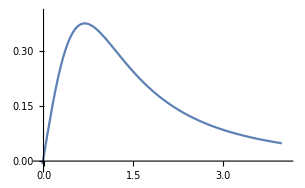
Assumption often adopted in calculation of accreiton disks: g_z(r,z)=z/((r^2+z^2)^(3/2))
Where  g_z is the gravitaional force n in Figure 
-Graphics-

z_max=±r/(√2)=0.7r